# Parametric Plots of Curvilinear Coordinate Systems

Define a curvilinear coordinate system with respect to Cartesian coordinates (x,y,z)
 x = f(u,v,t)
y= g(u,v,t)
z = h(u,v,t)
for some functions f,g,h defining the coordinate system.

E.g. parabolic coordinates

```mathematica
x[u_,v_,t_] = u v Cos[t] 
y[u_,v_,t_]  = u v Sin[t]
z[u_,v_,t_]  = -0.5 (u^2 - v^2)
```

u v Cos[t]

u v Sin[t]

-0.5 (u^2-v^2)

Now decide the coordinate surface you wish to plot (constant u,v or t) and plot....

E.g. Constant t=ϕ is a parabola rotated around the z-axis. Move the slider to adjust t=ϕ between the range 0 and 2π

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,t],y[u,v,t] ,z[u,v,t] },{u,0,2},{v,0,2π}],{t,0,2π}]
```

Now plot constant v and u respectively.

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,t],y[u,v,t] ,z[u,v,t] },{u,0,2},{t,0,2π}],{v,-4,4}]
```

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,t],y[u,v,t] ,z[u,v,t] },{v,0,2},{t,0,2π}],{u,-4,4}]
```

The two surfaces plotted explicitly together. Intersecting at right angles

```mathematica
Manipulate[ParametricPlot3D[{{x[u,v,t],y[u,v,t] ,-z[u,v,t]},{x[u,v,t],y[u,v,t] ,z[u,v,t] }},{v,0,2},{t,0,2π}],{u,-4,4}]
```

You can repeat this for any definition of x,y,z, making sure to adjust the ranges of u,v,t appropriately...

The meaning of these parametric plots are as follows:

In 2D (x,y), any point P can be expressed as some magnitude along the x direction, plus some magnitude along the y direction. Or, alternatively, this point P can be expressed as some position the upper surface and some position on the lower surface (if we only specified a position on the upper surface, we would have freedom to move anywhere along the lower surface and P would not be fixed).

```mathematica
Clear[u]
```

2D Hyperbolic Coordinates...

```mathematica
x[u_,v_] = v Exp[u]
y[u_,v_]  = v Exp[-u]
```

ⅇ^u v

ⅇ^-u v

Now lets plot some constant u/v lines that make up hyperbolic coordinates in two dimensions....

```mathematica
For[u=0,u<10,u++,Plot[u+v,{v,0,10}]]
```

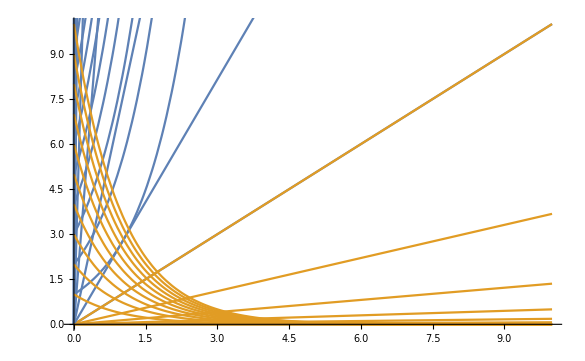

```mathematica
Show[Table[Plot[{x[u,v],y[u,v] },{v,0,10}],{u,0,10}],Table[Plot[{x[u,v],y[u,v] },{u,0,10}],{v,0,10}]]
```

```mathematica
For[u=0,u<10,u++,Plot[{x[u,v],y[u,v] },{v,0,10}] // Print]
```